```mathematica
data = Import["/net/home/f09/bajennissen/research/DAY189/morning_sec_int_data/675nm.dat"]
```

{{1.12389,0.216401},{1.13423,0.21793},{1.14739,0.215353},{1.16401,0.222423},{1.183,0.221302},{1.20042,0.223464},{1.22646,0.216723},{1.24828,0.206119},{1.27782,0.209612},{1.30453,0.205957},{1.34407,0.20872},{1.38078,0.193179},{1.41705,0.190786},{1.46132,0.185483},{1.51023,0.17823},{1.58758,0.164158},{1.63065,0.165006}}

0.356363-0.11715 x

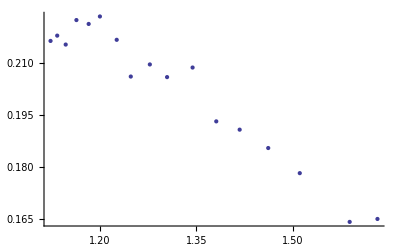

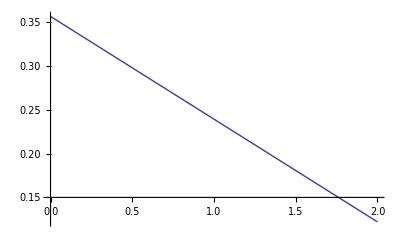

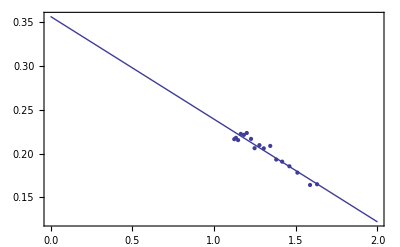

```mathematica
line = Fit[data,{1,x},x]
DataPlot=ListPlot[data]
FitPlot=Plot[line,{x,0,2}]
Show[DataPlot,FitPlot,PlotRange->All,Frame->True,AxesOrigin->{0,0}]
```